```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*INIITIALIZE PARAMETERS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

alpha = 0.5;
beta = 1.0;
delta = 0.5;
katta =5;
qAvg = 1.0;
eta = 0.25;
etaBar = 0.5;
chi = 0.1;
uBar = 1.0;

(*------------------------------------------------------------------------------------------------------------------------------*)
(*AGENTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Number of firms*)
n = 10.0;
(*A dummy vector used to identify each firm by a certain number: 1- first firm, 2-second firm,.....n- nth firm*)
Id = Table[i,{i,1,n}];
(*Number of consumers*)
m= 100.0;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PRICING*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*market share of the specialized firm*)
ms[t_,n_,q0_, qi_]:= q0 / Sum[qi[[t,i]],{i,1,n}];
(*markup smart components*)
etaSpec[delta_, etaSpecLag_, msSpec_, etaBar_]:=(1-delta)*etaSpecLag + delta*msSpec*etaBar;
(*price of specialist*)
pSpec[cs_,etaSpec_]:=(1+etaSpec)*cs;
(*price of firm if it produces the smart component*)
pFirmSelf[cSelf_,eta_]:=(1+eta)*cSelf;
(*price of firm if it produces the smart component*)
pFirmSpec[cSpec_,eta_]:=(1+eta)*cSpec;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*MARGINAL COSTS*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*Marginal costs of the "usual" component*)
cp = 20.0;
(*Marginal costs of the smart component*)
cs = 10.0;
(*Marginal costs if firm buys smart component from specialist*)
cSelf[cp_, cs_]:=cp + cs;
(*Marginal cost if firm buys smart component from specialist*)
cSpec[cp_,cs_, etaSpec_]:=cp + (1+etaSpec)*cs;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PROFIT*)
(*------------------------------------------------------------------------------------------------------------------------------*)
profit[q_,p_,c_]:=q*p - c*q;
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*QUALITY*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*quality of specialist*)
qualitySpec[t_,uBar_, alpha_, beta_,quantAggSpec_] :=uBar*(1+ beta*quantAggSpec^alpha);
(*quality of firm*)
qualityFirm[uBar_, alpha_, beta_,qFirm_ ] :=uBar*(1+ beta*qFirm^alpha);
```

SetDelayed::write: Tag List in {1., 11., 15.1421, 18.3205, 21.}[t_, uBar_, alpha_, beta_, quantAggSpec_] is Protected.

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*PROBABILITY*)
(*------------------------------------------------------------------------------------------------------------------------------*)

(*A function that computes the probability that consumer j buys from firm i*)
probability[i_,priceList_, qualityList_]:=Module[
{p =priceList, u = qualityList},
Exp[-chi*p[[i]]+ katta*u[[i]]]/Sum[Exp[-chi*p[[k]]+ katta*u[[k]]],{k,1,n}]];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------ EXERCISE 1 a) -------------------------------------------------------------*)
(*---------------------------------(*FIXED STRATEGIES: FIRMS PRODUCE SMART COMPONENT*)------------------------------------*)
```

Period Quantities: 11 | 13 | 11 | 11 | 12 | 11 | 9 | 6 | 8 | 8
7 | 44 | 5 | 6 | 19 | 15 | 2 | 0 | 1 | 1
0 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

Prices: 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5

Qualities: 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
4.31662 | 4.60555 | 4.31662 | 4.31662 | 4.4641 | 4.31662 | 4. | 3.44949 | 3.82843 | 3.82843
5.24264 | 8.54983 | 5. | 5.12311 | 6.56776 | 6.09902 | 4.31662 | 3.44949 | 4. | 4.
5.24264 | 13.53 | 5. | 5.12311 | 6.56776 | 6.09902 | 4.31662 | 3.44949 | 4. | 4.
5.24264 | 17.0312 | 5. | 5.12311 | 6.56776 | 6.09902 | 4.31662 | 3.44949 | 4. | 4.

Agg. Quantities: 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
11. | 13. | 11. | 11. | 12. | 11. | 9. | 6. | 8. | 8.
18. | 57. | 16. | 17. | 31. | 26. | 11. | 6. | 9. | 9.
18. | 157. | 16. | 17. | 31. | 26. | 11. | 6. | 9. | 9.
18. | 257. | 16. | 17. | 31. | 26. | 11. | 6. | 9. | 9.

Profits: 82.5 | 97.5 | 82.5 | 82.5 | 90. | 82.5 | 67.5 | 45. | 60. | 60.
52.5 | 330. | 37.5 | 45. | 142.5 | 112.5 | 15. | 0. | 7.5 | 7.5
0. | 750. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 750. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 750. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

Probs: 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.0932546 | 0.395427 | 0.0932546 | 0.0932546 | 0.194945 | 0.0932546 | 0.0191482 | 0.00122099 | 0.00812012 | 0.00812012
6.5841×10^-8 | 0.999945 | 1.95708×10^-8 | 3.62184×10^-8 | 0.0000496553 | 4.7654×10^-6 | 6.42212×10^-10 | 8.4085×10^-12 | 1.31867×10^-10 | 1.31867×10^-10
1.00996×10^-18 | 1. | 3.00205×10^-19 | 5.5557×10^-19 | 7.61685×10^-16 | 7.30986×10^-17 | 9.85117×10^-21 | 1.28982×10^-22 | 2.02277×10^-21 | 2.02277×10^-21
2.52015×10^-26 | 1. | 7.49098×10^-27 | 1.38631×10^-26 | 1.90062×10^-23 | 1.82402×10^-24 | 2.45815×10^-28 | 3.21846×10^-30 | 5.04738×10^-29 | 5.04738×10^-29

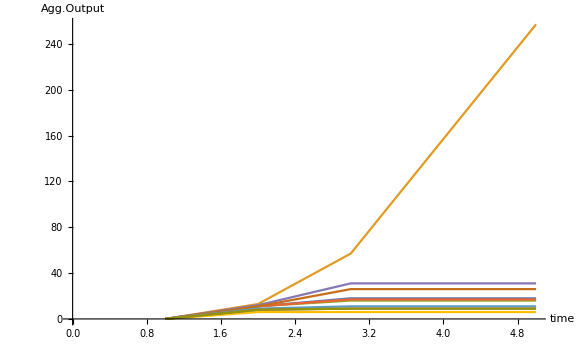

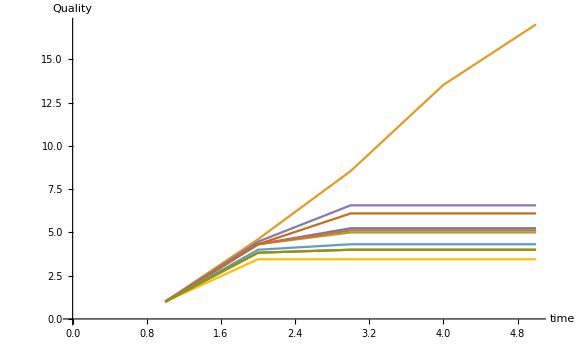

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*Batch Runs*)
(*------------------------------------------------------------------------------------------------------------------------------*)

R=20;
T = 5; (*100*)
count = 0;

Do[
count = count + 1;
(*Store Results in Lists such that 
e.g. priceList[[1,2]] gives the price of the second firm in period 1!!*)

(*prices*)
priceList =Table[Table[0.0,{i,1,n}],{i,1,T}];
qualityList =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*Quantities produced*)
quantPeriod =Table[Table[0.0,{i,1,n}],{i,1,T}];
quantAgg=Table[Table[0.0,{i,1,n}],{i,1,T}]; (*aggregated output*)
(*Profits*)
profitList =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*List of probabilities*)
probList =Table[Table[0.0,{i,1,n}],{i,1,T}];

(*PERIODS*)
Do[
(*compute prices*)
priceList[[t]] =Table[pFirmSelf[cSelf[cp,cs],eta],{i,1,n}];
(*compute aggregated output: depends on aggregate output and period output of LAST PERIOD*)
If[t==1,
quantAgg[[t]]=Table[0.0,{i,1,n}],
quantAgg[[t]]=Table[quantAgg[[t-1,i]]+ quantPeriod[[t-1,i]],{i,1,n}]];
(*compute quality using aggregated output*)
qualityList[[t]] =Table[qualityFirm[uBar, alpha, beta,quantAgg[[t,i]]],{i,1,n}];
(*Compute the probabilities and append them to a list! 
Since each consumer computes these probabilities the same way 
it is necessary to compute them for only one consumer*)
probList[[t]] = Table[probability[i,priceList[[t]], qualityList[[t]]],{i,1,n}];
(*compute demand*)
choiceListAll = RandomChoice[probList[[t]] ->Id,m];
(*Compute quantities produced in period t*)
quantPeriod[[t]] = Table[Count[choiceListAll,i],{i,1,n}];
(*compute profits*)
profitList[[t]] =Table[profit[quantPeriod[[t,i]],priceList[[t,i]],cSelf[cp,cs]],{i,1,n}],

{t,1,T}
];
,{r,1,R}]

(*------------------------------------------------------------------------------------------------------------------------------*)
(*Results*)
(*------------------------------------------------------------------------------------------------------------------------------*)
Print["Period Quantities: ", TableForm[quantPeriod]]
Print["Prices: ",TableForm[priceList]]
Print["Qualities: ",TableForm[qualityList]]
Print["Agg. Quantities: ",TableForm[quantAgg]]
Print["Profits: ",TableForm[profitList]]
Print["Probs: ",TableForm[probList]]

ListPlot[Table[Table[quantAgg[[t,j]],{t,1,5}],{j,1,n}],PlotRange->All,Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Agg.Output]}]
ListPlot[Table[Table[qualityList[[t,j]],{t,1,5}],{j,1,n}],PlotRange->All,Joined->True, ImageSize->Large,AxesLabel->{HoldForm[time],HoldForm[Quality]}]
```

```mathematica
(*count*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------ EXERCISE 1 c) -------------------------------------------------------------*)
(*---------------------------------(*FIXED STRATEGIES: FIRMS BUY SMART COMPONENT*)-----------------------------------------*)
```

```mathematica
T=5;
R=20;
count=0;
Do[
count=count+1;
(*prices*)
priceSpec =Table[0.0,{i,1,T}];
priceListFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
(*qualities*)
qualitySpec =Table[0.0,{i,1,T}];
qualityListFirm =Table[Table[0.0,{i,1,n}],{i,1,T}];
(*quantities produced*)
quantPeriodFirm =Table[Table[0.0,{i,1,n}],{i,1,T}];
quantPeriodSpec =Table[0.0,{i,1,T}];
quantAggFirm=Table[Table[0.0,{i,1,n}],{i,1,T}]; (*aggregated output of firm*)
quantAggSpec =Table[0.0,{i,1,T}];(*aggregated output of specialist*)
(*market share of specialist*)
msSpec= Table[0.0,{i,1,T}];
(*markup of specialist*)
markupSpec =Table[0.0,{i,1,T}];
(*profits*)
profitListFirm =Table[Table[0.0,{i,1,n}],{i,1,T}];
profitSpec = Table[0.0,{i,1,T}];
(*list of probabilities*)
probList =Table[Table[0.0,{i,1,n}],{i,1,T}];

(*PERIODS*)
Do[
(*compute markup*)
If[t==1,
markupSpec[[t]]=0.0,
markupSpec[[t]] = etaSpec[delta, markupSpec[[t-1]], msSpec[[t-1]], etaBar];
];
(*compute price of specialist*)
priceSpec[[t]]=pSpec[cs,markupSpec[[t]]];
(*compute prices of firms*)
priceListFirm[[t]] =Table[pFirmSpec[cSpec[cp,cs, markupSpec[[t]]],eta],{i,1,n}];
(*compute aggregated output of specialist: depends on aggregate output and period output of LAST PERIOD*)
If[t==1,
quantAggSpec[[t]]=0.0,
quantAggSpec[[t]]=quantAggSpec[[t-1]]+ quantPeriodSpec[[t-1]]];
(*compute quality using aggregated output*)
qualitySpec[[t]] =uBar*(1+ beta*quantAggSpec[[t]]^alpha);
qualityListFirm[[t]] =Table[qualitySpec[[t]],{i,1,n}];
(*Compute the probabilities and append them to a list! 
Since each consumer computes these probabilities the same way 
it is necessary to compute them for only one consumer*)
probList[[t]] = Table[probability[i,priceListFirm[[t]], qualityListFirm[[t]]],{i,1,n}];
(*compute demand*)
choiceListAll = RandomChoice[probList[[t]] ->Id,m];
(*compute quantities produced by firms in period t*)
quantPeriodFirm[[t]] = Table[Count[choiceListAll,i],{i,1,n}];
(*compute quantities produced by specialist in period t*)
quantPeriodSpec[[t]] =Sum[quantPeriodFirm[[t,i]],{i,1,n}];
(*compute market share*)
msSpec[[t]]=ms[t,n,quantPeriodSpec[[t]], quantPeriodFirm];
(*compute profits*)
profitListFirm[[t]] =Table[profit[quantPeriodFirm[[t,i]],priceListFirm[[t,i]],cSelf[cp,cs]],{i,1,n}];
profitSpec[[t]]=profit[quantPeriodSpec[[t]],priceSpec[[t]],cs],
{t,1,T}
];
,{r,1,R}];

Print["Period Quantities: ", TableForm[quantPeriodFirm]]
Print["Prices: ",TableForm[priceListFirm]]
Print["Market Share: ",TableForm[msSpec]]
Print["Profit Firms: ",TableForm[profitListFirm]]
Print["Profit Specialist: ",TableForm[profitSpec]]
Print["Agg. Quantities: ",TableForm[quantAggSpec]]
Print["Probs: ",TableForm[probList]]
```

Period Quantities: 5 | 16 | 12 | 13 | 10 | 9 | 12 | 8 | 9 | 6
6 | 9 | 10 | 11 | 10 | 10 | 10 | 11 | 11 | 12
11 | 7 | 4 | 7 | 12 | 11 | 5 | 21 | 14 | 8
7 | 5 | 5 | 13 | 13 | 7 | 10 | 11 | 15 | 14
9 | 11 | 8 | 12 | 9 | 11 | 11 | 8 | 14 | 7

Prices: 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625 | 40.625
42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875 | 42.1875
42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688 | 42.9688
43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594 | 43.3594

Market Share: 1
1
1
1
1

Profit Firms: 37.5 | 120. | 90. | 97.5 | 75. | 67.5 | 90. | 60. | 67.5 | 45.
63.75 | 95.625 | 106.25 | 116.875 | 106.25 | 106.25 | 106.25 | 116.875 | 116.875 | 127.5
134.063 | 85.3125 | 48.75 | 85.3125 | 146.25 | 134.063 | 60.9375 | 255.938 | 170.625 | 97.5
90.7813 | 64.8438 | 64.8438 | 168.594 | 168.594 | 90.7813 | 129.688 | 142.656 | 194.531 | 181.563
120.234 | 146.953 | 106.875 | 160.313 | 120.234 | 146.953 | 146.953 | 106.875 | 187.031 | 93.5156

Profit Specialist: 0.
250.
375.
437.5
468.75

Agg. Quantities: 0.
100.
200.
300.
400.

Probs: 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1

```mathematica
count
```

20